```mathematica
SetDirectory[NotebookDirectory[]]
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Chapter"],ShowGroupOpener->True],Cell[StyleData["Section"],ShowGroupOpener->True],Cell[StyleData["Subsection"],ShowGroupOpener->True],Cell[StyleData["Subsubsection"],ShowGroupOpener->True]}]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc

# Self-consistent Freeze-out curve

## Freeze-out Andronic et al.

```mathematica
Solve[mub==p3/(1+p4 sqrts),{sqrts}]
```

{{sqrts→(-mub+p3)/(mub p4)}}

```mathematica
Tcf/(1+Exp[p1-Log[sqrts]/p2])/.{sqrts->(-mub+p3)/(mub p4)}
```

Tcf/(1+ⅇ^(p1-Log[(-mub+p3)/(mub p4)]/p2))

```mathematica
T1[mub_]:=159/(1+ⅇ^(3.273-Log[(-mub+1386)/(mub 0.373)]/0.373));
```

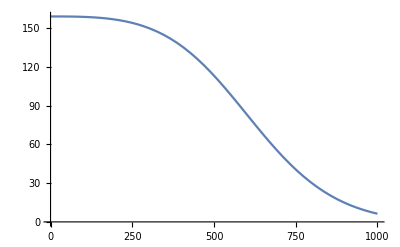

```mathematica
Plot[T1[x],{x,0,1000}]
```

```mathematica
Solve[mub==(13075/10)/(1+288/1000 sqrts),{sqrts}]
```

{{sqrts→-(125 (-2615+2 mub))/(72 mub)}}

```mathematica
(13075/10)/(1+288/1000 sqrts)/.{sqrts->3}//N
```

701.448

```mathematica
(13075/10)/(1+288/1000 sqrts)/.{sqrts->2}//N
```

829.632

```mathematica
(13075/10)/(1+288/1000 sqrts)/.{sqrts->1.6}//N
```

895.058

## Constant condensate

```mathematica
mubsigma={500.0,503.35570469798654,506.7114093959732,510.06711409395973,513.4228187919464,516.7785234899329,520.1342281879195,523.489932885906,526.8456375838925,530.2013422818792,533.5570469798657,536.9127516778524,540.2684563758389,543.6241610738255,546.9798657718121,550.3355704697987,553.6912751677853,557.0469798657718,560.4026845637584,563.7583892617449,567.1140939597315,570.4697986577181,573.8255033557047,577.1812080536913,580.5369127516778,583.8926174496644,587.248322147651,590.6040268456376,593.9597315436242,597.3154362416108,600.6711409395973,604.0268456375838,607.3825503355704,610.738255033557,614.0939597315436,617.4496644295302,620.8053691275168,624.1610738255033,627.51677852349,630.8724832214766,634.2281879194632,637.5838926174497,640.9395973154362,644.2953020134228,647.6510067114093,651.0067114093961,654.3624161073826,657.7181208053692,661.0738255033557,664.4295302013422,667.7852348993289,671.1409395973154,674.4966442953021,677.8523489932886,681.2080536912752,684.5637583892617,687.9194630872482,691.275167785235,694.6308724832215,697.9865771812081,701.3422818791946,704.6979865771812,708.0536912751677,711.4093959731545,714.765100671141,718.1208053691275,721.4765100671141,724.8322147651006,728.1879194630872,731.5436241610739,734.8993288590605,738.255033557047,741.6107382550335,744.9664429530201,748.3221476510067,751.6778523489934,755.0335570469799,758.3892617449665,761.7449664429531,765.1006711409395,768.4563758389262,771.8120805369127,775.1677852348994,778.5234899328858,781.8791946308725,785.2348993288591,788.5906040268457,791.9463087248323,795.3020134228187,798.6577181208054,802.013422818792,805.3691275167785,808.7248322147651,812.0805369127517,815.4362416107383,818.7919463087247,822.1476510067114,825.503355704698,828.8590604026846,832.2147651006712,835.5704697986577,838.9261744966443,842.281879194631,845.6375838926174,848.993288590604,852.3489932885906,855.7046979865772,859.0604026845637,862.4161073825503,865.771812080537,869.1275167785235,872.4832214765102,875.8389261744966,879.1946308724832,882.5503355704699,885.9060402684563,889.261744966443,892.6174496644295,895.9731543624162,899.3288590604026,902.6845637583892,906.0402684563759,909.3959731543624,909.655453475393,909.3959731543624,906.369829995247,906.0402684563759,904.0441681823193,902.6845637583892,901.0027841435648,899.3288590604026,897.7521937416426,895.9731543624162,894.3539744155507,892.6174496644295,890.8366981849324,889.261744966443,887.2192304359543,885.9060402684563,883.515594969527,882.5503355704699,879.7367627677125,879.1946308724832,875.8915483304728,875.8389261744966,872.4832214765102,871.8428257479001,869.1275167785235,867.7376742652865,865.771812080537,863.5967348384949,862.4161073825503,859.4230913951485,859.0604026845637,855.7046979865772,855.1247950074045,852.3489932885906,850.7385271062409,848.993288590604,846.3397869537544,845.6375838926174,842.281879194631,841.8739853055182,838.9261744966443,837.2962545324569,835.5704697986577,832.7195768795397,832.2147651006712,828.8590604026846,828.050316211101,825.503355704698,823.3251267356143,822.1476510067114,818.7919463087247,818.5886115335574,815.4362416107383,813.7321483843907,812.0805369127517,808.8932893630035,808.7248322147651,805.3691275167785,803.9392199027353,802.013422818792,798.9915637586515,798.6577181208054,795.3020134228187,793.9512220352563,791.9463087248323,788.9079897642503,788.5906040268457,785.2348993288591,783.7763094531131,781.8791946308725,778.6493144680254,778.5234899328858,775.1677852348994,773.4241657801355,771.8120805369127,768.4563758389262,768.2063414706549,765.1006711409395,762.9049836520878,761.7449664429531,758.3892617449665,757.5877081012687,755.0335570469799,752.2288696291929,751.6778523489934,748.3221476510067,746.8144465206682,744.9664429530201,741.6107382550335,741.3923815961001,738.255033557047,735.8966876035967,734.8993288590605,731.5436241610739,730.3775053570068,728.1879194630872,724.8437479876578,724.8322147651006,721.4765100671141,719.2310119065583,718.1208053691275,714.765100671141,713.602772697829,711.4093959731545,708.0536912751677,707.9563416177862,704.6979865771812,702.2418127895096,701.3422818791946,697.9865771812081,696.5031998061592,694.6308724832215,691.275167785235,690.7434343600063,687.9194630872482,684.9420449650352,684.5637583892617,681.2080536912752,679.0935633051051,677.8523489932886,674.4966442953021,673.2218908120083,671.1409395973154,667.7852348993289,667.3255718105156,664.4295302013422,661.3890860140303,661.0738255033557,657.7181208053692,655.4077690396028,654.3624161073826,651.0067114093961,649.400717380954,647.6510067114093,644.2953020134228,643.3668943789088,640.9395973154362,637.5838926174497,637.3053726353469,634.2281879194632,631.2018708581936,630.8724832214766,627.51677852349,625.0599867554441,624.1610738255033,620.8053691275168,618.8901112703542,617.4496644295302,614.0939597315436,612.6915825328542,610.738255033557,607.3825503355704,606.4638133707324,604.0268456375838,600.6711409395973,600.20628395113,597.3154362416108,593.9597315436242,593.9185367521599,590.6040268456376,587.5879062943097,587.248322147651,583.8926174496644,581.2263439455628,580.5369127516778,577.1812080536913,574.8349487473745,573.8255033557047,570.4697986577181,568.4134072099965,567.1140939597315,563.7583892617449,561.9614488250608,560.4026845637584,557.0469798657718,555.4788420735641,553.6912751677853,550.3355704697987,548.9653908728498,546.9798657718121,543.6241610738255,542.4209304945948,540.2684563758389,536.9127516778524,535.8453242538963,533.5570469798657,530.2013422818792,529.238459574326,526.8456375838925,523.489932885906,522.6002443002506,520.1342281879195,516.7785234899329,515.9306025946404,513.4228187919464,510.06711409395973,509.22947095313765,506.7114093959732,503.35570469798654,502.4967939216212,500.0};
Tsigma={NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,14.545454545454547,14.664156743289569,15.75757575757576,16.263208870701384,16.96969696969697,17.600131585471228,18.181818181818183,18.859615039224852,19.393939393939394,20.066987009172436,20.606060606060606,21.234439935383385,21.81818181818182,22.36982283015845,23.030303030303028,23.478720824564466,24.242424242424242,24.565308105347135,25.454545454545457,25.63279832134959,26.666666666666664,26.68371707533457,27.691160644752365,27.87878787878788,28.685672625916784,29.090909090909093,29.671673770280034,30.303030303030305,30.64997076582657,31.51515151515152,31.62121702295617,32.56719160064101,32.72727272727273,33.49566402726068,33.93939393939394,34.4217020095107,35.15151515151515,35.34526769322902,36.25546400378842,36.36363636363637,37.14369728002372,37.57575757575758,38.0324946004603,38.78787878787879,38.92148930151597,39.792049303581535,40.0,40.651803460539995,41.21212121212121,41.51378002936995,42.373285545971044,42.42424242424242,43.2088725448678,43.63636363636364,44.0481723397005,44.84848484848485,44.89055566223026,45.70956433870868,46.060606060606055,46.52985673640479,47.27272727272727,47.35424117559981,48.159421386325796,48.484848484848484,48.9637834725064,49.696969696969695,49.772964938912615,50.56348774388485,50.909090909090914,51.35449275825037,52.121212121212125,52.150827989345075,52.92626916190007,53.33333333333333,53.70606855094294,54.48798065226239,54.54545454545455,55.25175261513313,55.75757575757576,56.0221480120809,56.787668822535146,56.96969696969697,57.54345060344023,58.18181818181819,58.30595443464398,59.05531064568237,59.3939393939394,59.80445312731569,60.557628734076495,60.60606060606061,61.293843036751625,61.81818181818181,62.037481251440354,62.77406297523998,63.03030303030304,63.50584320261153,64.24242424242425,64.24493638499132,64.96539276323992,65.45454545454545,65.69358112080096,66.41611514017403,66.66666666666667,67.13375331455784,67.85801218072884,67.87878787878788,68.56545219628904,69.0909090909091,69.28103387584629,69.98869152616514,70.3030303030303,70.69485965244019,71.40349425688501,71.51515151515152,72.1005642673133,72.72727272727273,72.80591486698206,73.49817714020813,73.93939393939394,74.19510678259591,74.88773506480089,75.15151515151516,75.57652604297455,76.26928180742773,76.36363636363636,76.95021227294873,77.57575757575758,77.63978488255361,78.31621055071426,78.78787878787878,78.99848722256378,79.67457102343569,80.0,80.34980169411901,81.02534832805414,81.21212121212122,81.69377883373612,82.36860127460263,82.42424242424242,83.03047300273477,83.63636363636364,83.7014193792572,84.35994193677583,84.84848484848484,85.02478713196888,85.6822473893082,86.06060606060606,86.34120965394861,86.99745286314206,87.27272727272728,87.6507470912156,88.30562532711028,88.48484848484848,88.95346239610261,89.60683396548134,89.6969696969697,90.24942080859381,90.90115013032914,90.9090909090909,91.53868969793774,92.12121212121211,92.18586115433958,92.82133836710085,93.33333333333333,93.46381109702695,94.09743783867013,94.54545454545455,94.73539746966796,95.36706053111841,95.75757575757576,96.00068921792128,96.6302801099795,96.96969696969697,97.25975645144871,97.8871711758152,98.18181818181819,98.51267021149798,99.13780905596113,99.39393939393939,99.75950218818025,100.3822694193129,100.6060606060606,101.0003244337213,101.62062807330629,101.81818181818183,102.23520905383897,102.85296059741628,103.03030303030303,103.46422786670956,104.07934199627036,104.24242424242425,104.68745210198469,105.29984633245677,105.45454545454545,105.9049519148846,106.51454632290815,106.66666666666666,107.11679609324885,107.72351295012425,107.87878787878788,108.32305155494312};
```

```mathematica
mubsigma2=mubsigma[[124;;-1]];
Tsigma2=Tsigma[[124;;-1]];
```

```mathematica
intsigma=Interpolation[Transpose[{mubsigma2,Tsigma2}]]
```

InterpolatingFunction[…]

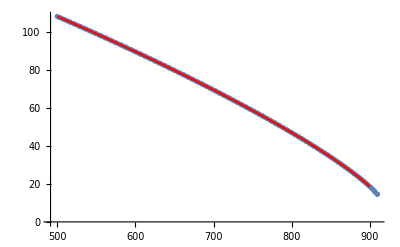

```mathematica
Show[ListPlot[Transpose[{mubsigma2,Tsigma2}]],Plot[intsigma[x],{x,500,900},PlotStyle->Red]]
```

## lines compare

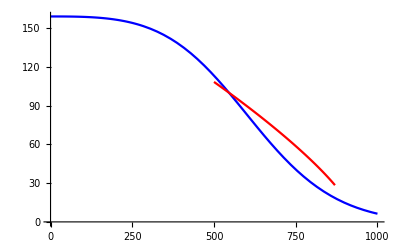

```mathematica
Show[Plot[{T1[x]},{x,0,1000},PlotStyle->Blue],Plot[intsigma[x],{x,500,870},PlotStyle->Red],Plot[TlineYL[157,0.0153,0.96*10^-3,x],{x,0,870},PlotStyle->Black]]
```

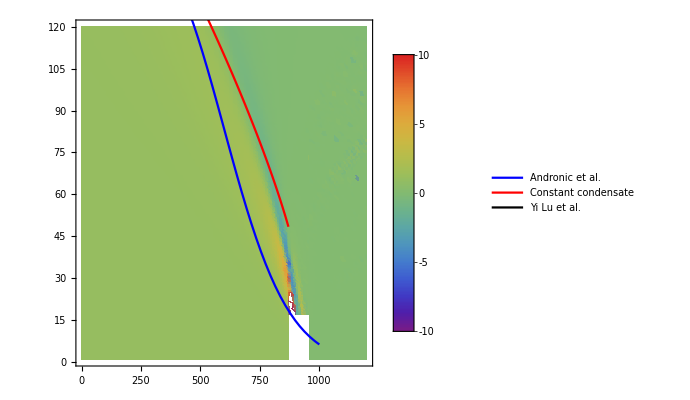

```mathematica
Show[ListDensityPlot[{r42low,r42high,r42high3},PlotRange->{{0,1200},All,{-10,10}},ColorFunction->"Rainbow",PlotLegends->Automatic],Plot[{T1[x]},{x,0,1000},PlotStyle->Blue,PlotLegends->{"Andronic et al."}],Plot[intsigma[x]+20,{x,500,870},PlotStyle->Red,PlotLegends->{"Constant condensate"}],Plot[TlineYL[157,0.0153,0.96*10^-3,x],{x,0,870},PlotStyle->Black,PlotLegends->{"Yi Lu et al."}]]
```

## PDM data

```mathematica
r42low=Import["./phasedata_v2/r42low.dat"];
r42low2=Import["./phasedata_v2/datav4/r42low800to870.dat"];
r42high=Import["./phasedata_v3/datav3/r42high.dat"];
r42high2=Import["./phasedata_v4/r42high2.dat"];
r42high3=Import["./phasedata_v5/r42high3.dat"];
r21low=Import["./phasedata_v2/r21low.dat"];
r32low=Import["./phasedata_v2/r32low.dat"];
r31low=Import["./phasedata_v2/r31low.dat"];
```

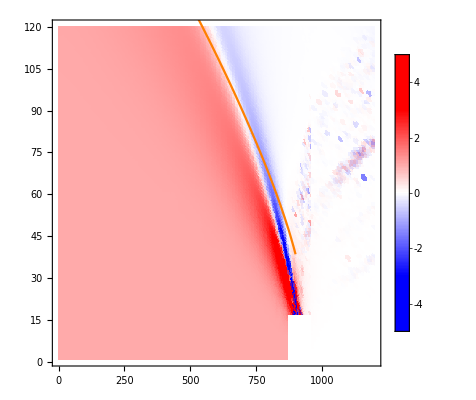

```mathematica
ConditionalPlotColor[val_]:=Which[val>0,Blend[{White,Red},val/3],(*正值：白到红渐变*)val<0,Blend[{White,Blue},Abs[val/(-3)]],(*负值：白到蓝渐变*)True,White (*0 处为白*)]
Show[ListDensityPlot[{r42low,r42low2,r42high,r42high3},PlotRange->{{0,1200},All,{-5,5}},ColorFunctionScaling->False,ColorFunction->(ConditionalPlotColor[#1]&),PlotLegends->Automatic,ClippingStyle->Automatic],Plot[{(*T1[x]*)(*+13.5,T1[x],T1[x]-14*)},{x,0,1200},PlotStyle->{Red,Blue,Red}],Plot[{(*intsigma[x],intsigma[x]-5,*)intsigma[x]+20},{x,500,900},PlotStyle->Orange]]
```

```mathematica
f=Interpolation[Flatten[{r42low(*,r42high*)(*,r42high3*)},1],InterpolationOrder->3];
f2=Interpolation[Flatten[{r42low2(*,r42high*)(*,r42high3*)},1],InterpolationOrder->3];
f3=Interpolation[Flatten[{r42high(*,r42high3*)},1],InterpolationOrder->3];
f21=Interpolation[Flatten[{r21low(*,r42high*)(*,r42high3*)},1],InterpolationOrder->3];
f31=Interpolation[Flatten[{r31low(*,r42high*)(*,r42high3*)},1],InterpolationOrder->3];
```

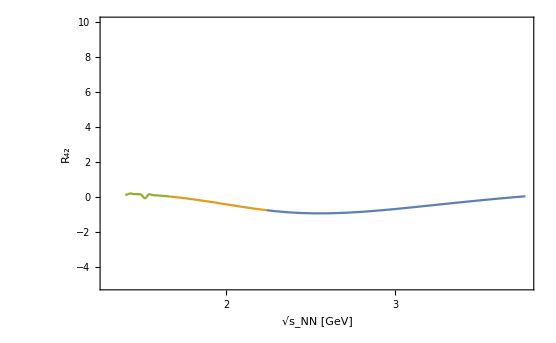

```mathematica
l=25;
ListLinePlot[{Table[Transpose[{-(125. (-2615.+2. x))/(72. x),f[x,intsigma[x]+l]}],{x,600,800}],Table[Transpose[{-(125. (-2615.+2. x))/(72. x),f2[x,intsigma[x]+l]}],{x,800,870}],Table[Transpose[{-(125. (-2615.+2. x))/(72. x),f3[x,intsigma[x]+l]}],{x,870,900}]},PlotRange->{All,{-5,10}},ScalingFunctions->{"Log"},Frame->True,FrameLabel->{"√s_NN [GeV]","R_42"},FrameStyle->Directive[Black,12],LabelStyle->Directive[14]]
```

## STAR DATA

## BES I data

```mathematica
sqrtsBESI={7.7,11.5,14.5,19.6,27,39,54.4,62.4,200};
R42BESIcen={1.76697,0.695796,1.46876,0.140553,0.196254,0.739693,0.632837,0.792955,0.900669};
R42BESIstaterr={1.15082,0.595077,0.395981,0.328768,0.219415,0.147006,0.0553742,0.250823,0.208458};
R42BESIsyserr={0.413944, 0.266722, 0.254053, 0.155986, 0.143158, 0.135754, 0.138702, 0.121927, 0.139363};

R21BESIcen={0.937634, 0.965991, 1.02136, 1.10972, 1.29862, 1.67391, 2.13712, 2.35186, 6.6121};
R21BESIstaterr={0.00541433, 0.00338953, 0.00256581, 0.00266482, 0.00220565, 0.00175524, 0.000877283, 0.00385228, 0.00666528};
R21BESIsyserr={0.00848957, 0.0148582, 0.00729976, 0.00868959, 0.0110364,0.0145561, 0.0177191, 0.0427244, 0.0899917};
R21BESIerr=√(R21BESIstaterr^2+R21BESIsyserr^2);

R32BESIcen={0.798587, 0.783562, 0.782208, 0.642055, 0.553053, 0.4419, 0.346852, 0.325439, 0.122302};
R32BESIstaterr={0.0752691, 0.0417112, 0.0286995, 0.0255525, 0.0177318, 0.0114112, 0.00436123, 0.0185227, 0.0125973};
R32BESIsyserr={0.0341678, 0.035222, 0.0112016, 0.0171887, 0.0147127, 0.0151383, 0.00638463, 0.0155955, 0.0108993};

C1BESIcen={39.421539, 30.253971, 25.657473, 21.769468, 17.470406, 13.467374, 11.107300, 10.102587, 4.566216};
C1BESIstaterr={0.019992, 0.010611, 0.007130, 0.006680, 0.004497, 0.002624, 0.001083, 0.004055, 0.002280};
C1BESIsyserr={2.415359, 2.821748, 1.718524, 1.461477, 1.203613, 0.941084, 0.804850, 1.034544, 0.389982};

C2BESIcen={36.962982, 29.225075, 26.205402, 24.157978, 22.687414, 22.543184, 23.737600, 23.759876, 30.192270};
C2BESIstaterr={0.214242, 0.103085, 0.066157, 0.058211, 0.038547, 0.023513, 0.009564, 0.038164, 0.026632};
C2BESIsyserr={2.034195, 2.338558, 1.599479, 1.466974, 1.443992, 1.480664, 1.573370, 2.147386, 2.423239};

C3BESIcen={29.518143, 22.899647, 20.498066, 15.510752, 12.547338, 9.961836, 8.233450, 7.732394, 3.692589};
C3BESIstaterr={2.839415, 1.242016, 0.765315, 0.627572, 0.407553, 0.260202, 0.104189, 0.444216, 0.382348};
C3BESIsyserr={1.654657, 1.362639, 1.153057, 0.678157, 0.623777, 0.506266, 0.418713, 0.575012, 0.390343};

C4BESIcen={65.312561, 20.334698, 38.489456, 3.395470, 4.452486, 16.675041, 15.022000, 18.840511, 27.193245};
C4BESIstaterr={43.465191, 17.619955, 10.460115, 8.052210, 5.031746, 3.355528, 1.322940, 6.029626, 6.346742};
C4BESIsyserr={16.201504, 7.371407, 8.062140, 3.662928, 3.098153, 3.343535, 2.948390, 3.992425, 4.891671};

R31BESIcen=C3BESIcen/C1BESIcen;
R31BESIerr=√((C3BESIcen/C1BESIcen √((C3BESIstaterr/C3BESIcen)^2+(C1BESIstaterr/C1BESIcen)^2))^2+(C3BESIcen/C1BESIcen √((C3BESIsyserr/C3BESIcen)^2+(C1BESIsyserr/C1BESIcen)^2))^2);
```

## BES II data

```mathematica
sqrtsBESII={7.7,9.2,11.5,14.6,17.3,19.6};

C1BESIIcen={41.2105,36.6996,32.3236,27.7652,24.5968,22.8157};
C1BESIIstaterr={0.00438596,0.00324747,0.00259436,0.00205992,0.00232622,0.0014898};
C1BESIIsyserr={1.0748,1.04658,0.916706,0.78121,0.726908,0.677734};

C2BESIIcen={36.5726,32.9205,29.6044,26.9923,25.4113,24.8554};
C2BESIIstaterr={0.0469661,0.0331665,0.0246947,0.0189902,0.02098350,0.0131521};
C2BESIIsyserr={0.829231,0.806224,0.726638,0.678691,0.684972,0.687093};

C3BESIIcen={27.1902,24.6593,21.2265,18.2849,16.5894,15.4993};
C3BESIIstaterr={0.598839,0.41511,0.294553,0.215427,0.234402,0.143585};
C3BESIIsyserr={0.48419,0.548797,0.456783,0.326358,0.247559,0.266326};

C4BESIIcen={15.0646,18.0272,11.0531,11.4859,8.88054,8.10012};
C4BESIIstaterr={9.0936,6.05982,4.09523,2.82486,3.07383,1.83483};
C4BESIIsyserr={4.74059,2.5035,1.80857,1.27389,1.90021,0.900393};

R21BESIIcen={0.88849,0.897983,0.916325,0.972529,1.03338,1.08976};
R21BESIIstaterr={0.00113623,0.000900635,0.000762608,0.000683388,0.000850682,0.000575278};
R21BESIIsyserr={0.00303328,0.00378717,0.00361941,0.00322545,0.00324246,0.00310216};
R21BESIIerr=√(R21BESIIstaterr^2+R21BESIIsyserr^2);

R31BESIIcen={0.66417,0.675786,0.658088,0.660095,0.675256,0.680595};
R31BESIIstaterr={0.0145063,0.011283,0.00908288,0.00772972,0.0094888,0.0062675};
R31BESIIsyserr={0.00990556,0.00980052,0.0097405,0.00845133,0.011269,0.00835287};
R31BESIIerr=√(R31BESIIstaterr^2+R31BESIIsyserr^2);

R42BESIIcen={0.417735,0.550703,0.381199,0.430751,0.356063,0.328484};
R42BESIIstaterr={0.246897,0.183197,0.137369,0.104085,0.120039,0.0733153};
R42BESIIsyserr={0.134838,0.0739699,0.0537708,0.0403519,0.0795194,0.0404057};

R32BESIIcen={0.745662,0.751448,0.717843,0.678434,0.653356,0.624267};
R32BESIIstaterr={0.0161972,0.0124714,0.00982302,0.00788677,0.00910491,0.0057064};
R32BESIIsyserr={0.00989561,0.00959875,0.00859547,0.00703623,0.00944456,0.00655348};
```

## Fixed-Target data

```mathematica
sqrtsFT={3,3.2,3.5,3.9};
R21FTcen={1.217,1.135,1.094,1.075};
R21FTup={1.238,1.150,1.118,1.092};
R21err=R21FTup-R21FTcen;

R31FTcen={1.163,1.086,1.055,1.101};
R31FTup={1.221,1.129,1.138,1.191};
R31err=R31FTup-R31FTcen;

R42FTcen={-0.843,-0.303,0.159,0.209};
R42FTup={-0.025,-0.119,0.292,0.370};
R42err=R42FTup-R42FTcen;
```

## Find freeze-out T & μ_B with PDM data

## peak of (χ^B)_2

```mathematica
chi2low=Import["./phasedata_v2/chi2low.dat"];
(*intchi2=Interpolation[chi2low,InterpolationOrder->3];*)
chi2peak=Flatten[Table[Position[chi2low[[i]],Max[chi2low[[i]]]],{i,63,87,1}]];
mubchi2=Table[i*10,{i,63,87}];
chipeakT=Transpose[{mubchi2,chi2peak}];
fchi2peak=Interpolation[chipeakT]
```

InterpolatingFunction[…]

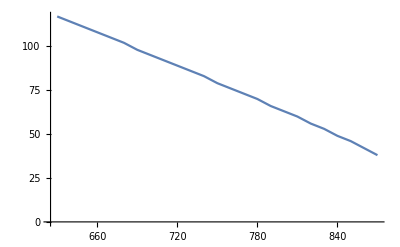

```mathematica
ListLinePlot[chipeakT]
```

## √s_NN=3 GeV

```mathematica
z21up=R21FTcen+R21err;
z21down=R21FTcen-R21err;
z31up=R31FTcen+R31err;
z31down=R31FTcen-R31err;
```

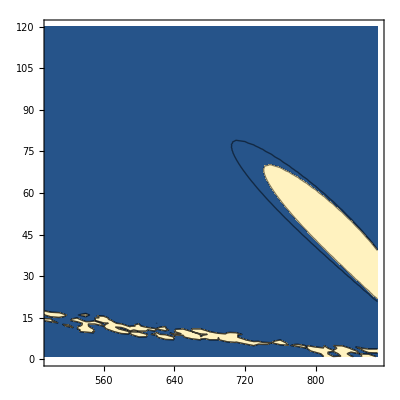

```mathematica
ListContourPlot[r21low,Contours->{z21up[[1]],z21down[[1]]},PlotRange->{{500,870},{0,120},All}]
```

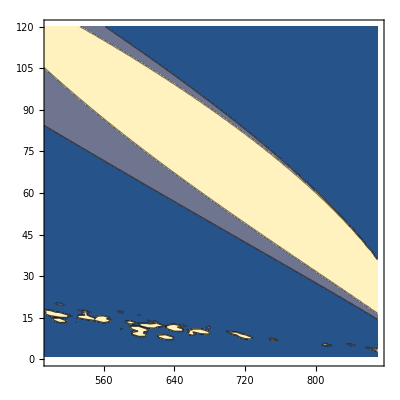

```mathematica
ListContourPlot[{r31low},Contours->{z31up[[1]],z31down[[1]]},PlotRange->{{500,870},{0,120},All}]
```

```mathematica
cp=ContourPlot[f21[x,y],{x,500,870},{y,40,120},Contours->{z21up[[1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f21[x,y],{x,500,870},{y,40,120},Contours->{z21down[[1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f31[x,y],{x,500,870},{y,40,120},Contours->{z31up[[1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f31[x,y],{x,500,870},{y,40,120},Contours->{z31down[[1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

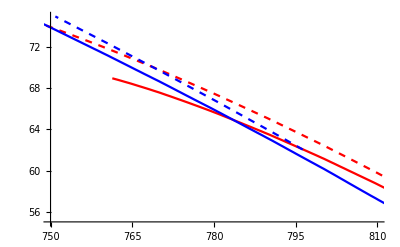

```mathematica
ListLinePlot[{R21up[[250;;-1]],R21down[[290;;-1]],R31up[[550;;-1]],R31down[[550;;-1]]},PlotRange->{{750,810},{55,75}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}]
```

```mathematica
intR21up=Interpolation[R21up[[250;;-1]],InterpolationOrder->1];
intR21down=Interpolation[R21down[[290;;-1]],InterpolationOrder->1];
intR31up=Interpolation[R31up[[550;;-1]],InterpolationOrder->1];
intR31down=Interpolation[R31down[[550;;-1]],InterpolationOrder->1];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,780}]
intR21up[x1]/.%
```

{x1→783.526}

64.9297

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,780}]
intR21down[x1]/.%
```

Interpolation::innd: {}⟦290;;-1⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦550;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {780.} 处，函数值 {Interpolation[{}⟦290;;-1⟧,InterpolationOrder→1.][780.]-1. Interpolation[{}⟦550;;-1⟧,InterpolationOrder→1.][780.]} 不是由数字组成的维度为 {1} 的列表.

FindRoot[intR21down[x1]==intR31down[x1],{x1,780}]

Interpolation::innd: {}⟦290;;-1⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦550;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {780.} 处，函数值 {Interpolation[{}⟦290;;-1⟧,InterpolationOrder→1.][780.]-1. Interpolation[{}⟦550;;-1⟧,InterpolationOrder→1.][780.]} 不是由数字组成的维度为 {1} 的列表.

ReplaceAll::reps: {FindRoot[intR21down[x1]==intR31down[x1],{x1,780}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Interpolation[{}⟦290;;-1⟧,InterpolationOrder→1][x1]/.FindRoot[intR21down[x1]==intR31down[x1],{x1,780}]

## √s_NN=3.2 GeV

```mathematica
z21up=R21FTcen+R21err;
z21down=R21FTcen-R21err;
z31up=R31FTcen+R31err;
z31down=R31FTcen-R31err;
```

```mathematica
ListContourPlot[{r21low},Contours->{z21up[[2]],z21down[[2]]},PlotRange->{{500,870},{0,120},All}]
```

-Graphics-

```mathematica
ListContourPlot[{r31low},Contours->{z31up[[2]],z31down[[2]]},PlotRange->{{500,870},{0,120},All}]
```

-Graphics-

```mathematica
cp=ContourPlot[f21[x,y],{x,500,870},{y,40,120},Contours->{z21up[[2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f21[x,y],{x,500,870},{y,40,120},Contours->{z21down[[2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f31[x,y],{x,500,870},{y,40,120},Contours->{z31up[[2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f31[x,y],{x,500,870},{y,40,120},Contours->{z31down[[2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

Interpolation::inord: 选项 InterpolationOrder -> 3. 的值应该是一个非负机器精度整数或者由整数组成的长度等于维度数 2 的列表.

General::stop: 在本次计算中，Interpolation::inord 的进一步输出将被抑制.

Interpolation::inord: 选项 InterpolationOrder -> 3. 的值应该是一个非负机器精度整数或者由整数组成的长度等于维度数 2 的列表.

General::stop: 在本次计算中，Interpolation::inord 的进一步输出将被抑制.

Interpolation::inord: 选项 InterpolationOrder -> 3. 的值应该是一个非负机器精度整数或者由整数组成的长度等于维度数 2 的列表.

General::stop: 在本次计算中，Interpolation::inord 的进一步输出将被抑制.

Interpolation::inord: 选项 InterpolationOrder -> 3. 的值应该是一个非负机器精度整数或者由整数组成的长度等于维度数 2 的列表.

General::stop: 在本次计算中，Interpolation::inord 的进一步输出将被抑制.

```mathematica
ListLinePlot[{R21up[[380;;-1]],R21down[[1;;-530]],R31up[[400;;-1]],R31down[[400;;-1]]},PlotRange->{{650,790},{72,100}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}]
```

Part::take: 无法在 {} 中提取位置 380 至 -1.

Part::take: 无法在 {} 中提取位置 1 至 -530.

Part::take: 无法在 {} 中提取位置 400 至 -1.

General::stop: 在本次计算中，Part::take 的进一步输出将被抑制.

-Graphics-

```mathematica
intR21up=Interpolation[R21up[[380;;-1]],InterpolationOrder->1];
intR21down=Interpolation[R21down[[1;;-530]],InterpolationOrder->1];
intR31up=Interpolation[R31up[[400;;-1]],InterpolationOrder->1];
intR31down=Interpolation[R31down[[400;;-1]],InterpolationOrder->1];
```

Part::take: 无法在 {} 中提取位置 380 至 -1.

Interpolation::innd: {}⟦380;;-1⟧ 中的第一个参数不包含数据和坐标列表.

Part::take: 无法在 {} 中提取位置 1 至 -530.

Interpolation::innd: {}⟦1;;-530⟧ 中的第一个参数不包含数据和坐标列表.

Part::take: 无法在 {} 中提取位置 400 至 -1.

Interpolation::innd: {}⟦400;;-1⟧ 中的第一个参数不包含数据和坐标列表.

Part::take: 无法在 {} 中提取位置 400 至 -1.

Interpolation::innd: {}⟦400;;-1⟧ 中的第一个参数不包含数据和坐标列表.

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,680}]
intR21up[x1]/.%
```

Interpolation::innd: {}⟦380;;-1⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦400;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {680.} 处，函数值 {Interpolation[{}⟦380;;-1⟧,InterpolationOrder→1.][680.]-1. Interpolation[{}⟦400;;-1⟧,InterpolationOrder→1.][680.]} 不是由数字组成的维度为 {1} 的列表.

FindRoot[intR21up[x1]==intR31up[x1],{x1,680}]

Interpolation::innd: {}⟦380;;-1⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦400;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {680.} 处，函数值 {Interpolation[{}⟦380;;-1⟧,InterpolationOrder→1.][680.]-1. Interpolation[{}⟦400;;-1⟧,InterpolationOrder→1.][680.]} 不是由数字组成的维度为 {1} 的列表.

ReplaceAll::reps: {FindRoot[intR21up[x1]==intR31up[x1],{x1,680}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Interpolation[{}⟦380;;-1⟧,InterpolationOrder→1][x1]/.FindRoot[intR21up[x1]==intR31up[x1],{x1,680}]

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,720}]
intR21down[x1]/.%
```

Interpolation::innd: {}⟦1;;-530⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦400;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {720.} 处，函数值 {Interpolation[{}⟦1;;-530⟧,InterpolationOrder→1.][720.]-1. Interpolation[{}⟦400;;-1⟧,InterpolationOrder→1.][720.]} 不是由数字组成的维度为 {1} 的列表.

FindRoot[intR21down[x1]==intR31down[x1],{x1,720}]

Interpolation::innd: {}⟦1;;-530⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦400;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {720.} 处，函数值 {Interpolation[{}⟦1;;-530⟧,InterpolationOrder→1.][720.]-1. Interpolation[{}⟦400;;-1⟧,InterpolationOrder→1.][720.]} 不是由数字组成的维度为 {1} 的列表.

ReplaceAll::reps: {FindRoot[intR21down[x1]==intR31down[x1],{x1,720}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Interpolation[{}⟦1;;-530⟧,InterpolationOrder→1][x1]/.FindRoot[intR21down[x1]==intR31down[x1],{x1,720}]

## √s_NN=3.5 GeV

```mathematica
z21up=R21FTcen+R21err;
z21down=R21FTcen-R21err;
z31up=R31FTcen+R31err;
z31down=R31FTcen-R31err;
```

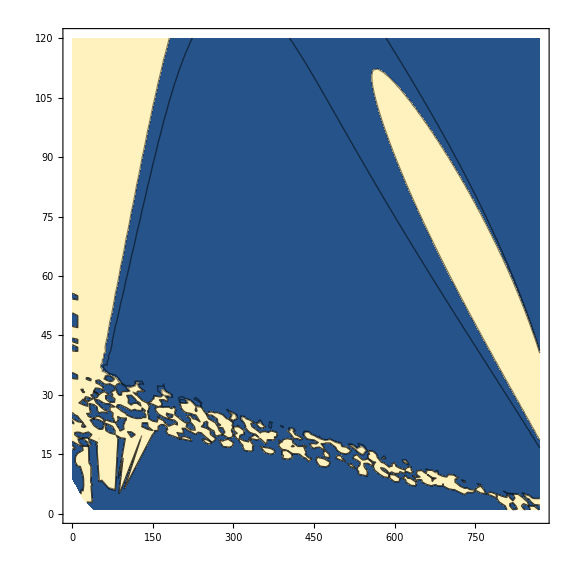

```mathematica
ListContourPlot[{r21low},Contours->{z21up[[3]],z21down[[3]]},PlotRange->{{0,870},{0,120},All}]
```

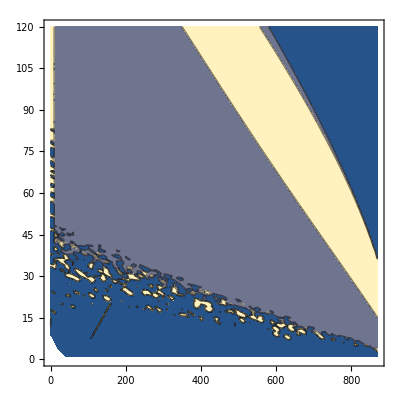

```mathematica
ListContourPlot[{r31low},Contours->{z31up[[3]],z31down[[3]]},PlotRange->{{0,870},{0,120},All}]
```

```mathematica
cp=ContourPlot[f21[x,y],{x,500,870},{y,40,120},Contours->{z21up[[3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f21[x,y],{x,500,870},{y,40,120},Contours->{z21down[[3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f31[x,y],{x,500,870},{y,40,120},Contours->{z31up[[3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[f31[x,y],{x,500,870},{y,40,120},Contours->{z31down[[3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

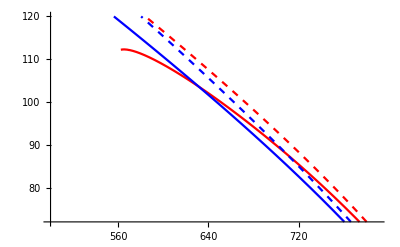

```mathematica
ListLinePlot[{R21up[[520;;-1]],R21down[[432;;-1]],R31up[[1;;-500]],R31down[[1;;-1]]},PlotRange->{{500,790},{72,120}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}]
```

```mathematica
intR21up=Interpolation[R21up[[520;;-1]],InterpolationOrder->1];
intR21down=Interpolation[R21down[[432;;-1]],InterpolationOrder->1];
intR31up=Interpolation[R31up[[1;;-500]],InterpolationOrder->1];
intR31down=Interpolation[R31down[[1;;-1]],InterpolationOrder->1];
```

Part::take: 无法在 {} 中提取位置 520 至 -1.

Interpolation::innd: {}⟦520;;-1⟧ 中的第一个参数不包含数据和坐标列表.

Part::take: 无法在 {} 中提取位置 432 至 -1.

Interpolation::innd: {}⟦432;;-1⟧ 中的第一个参数不包含数据和坐标列表.

Part::take: 无法在 {} 中提取位置 1 至 -500.

Interpolation::innd: {}⟦1;;-500⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {} 中的第一个参数不包含数据和坐标列表.

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,630}]
intR21up[x1]/.%
```

Interpolation::innd: {}⟦1;;-500⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦520;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {630.} 处，函数值 {-1. Interpolation[{}⟦1;;-500⟧,InterpolationOrder→1.][630.]+Interpolation[{}⟦520;;-1⟧,InterpolationOrder→1.][630.]} 不是由数字组成的维度为 {1} 的列表.

FindRoot[intR21up[x1]==intR31up[x1],{x1,630}]

Interpolation::innd: {}⟦1;;-500⟧ 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦520;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {630.} 处，函数值 {-1. Interpolation[{}⟦1;;-500⟧,InterpolationOrder→1.][630.]+Interpolation[{}⟦520;;-1⟧,InterpolationOrder→1.][630.]} 不是由数字组成的维度为 {1} 的列表.

ReplaceAll::reps: {FindRoot[intR21up[x1]==intR31up[x1],{x1,630}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Interpolation[{}⟦520;;-1⟧,InterpolationOrder→1][x1]/.FindRoot[intR21up[x1]==intR31up[x1],{x1,630}]

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,600}]
intR21down[x1]/.%
```

Interpolation::innd: {} 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦432;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {600.} 处，函数值 {-1. Interpolation[{},InterpolationOrder→1.][600.]+Interpolation[{}⟦432;;-1⟧,InterpolationOrder→1.][600.]} 不是由数字组成的维度为 {1} 的列表.

FindRoot[intR21down[x1]==intR31down[x1],{x1,600}]

Interpolation::innd: {} 中的第一个参数不包含数据和坐标列表.

Interpolation::innd: {}⟦432;;-1⟧ 中的第一个参数不包含数据和坐标列表.

FindRoot::nlnum: 在 {x1} = {600.} 处，函数值 {-1. Interpolation[{},InterpolationOrder→1.][600.]+Interpolation[{}⟦432;;-1⟧,InterpolationOrder→1.][600.]} 不是由数字组成的维度为 {1} 的列表.

ReplaceAll::reps: {FindRoot[intR21down[x1]==intR31down[x1],{x1,600}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Interpolation[{}⟦432;;-1⟧,InterpolationOrder→1][x1]/.FindRoot[intR21down[x1]==intR31down[x1],{x1,600}]

## data on PDM phase diagram

```mathematica
mubhigh={783.526,710.942,631.444};
mublow={768.708,685.129,534.976};
mubcen=(mubhigh+mublow)/2;
muberr=(mubhigh-mublow)/2;
Th={64.9297,85.0404,103.611};
Tl={70.0825,92.9568,130.626};
Tcen=(Th+Tl)/2;
Terr=(-Th+Tl)/2;
```

```mathematica
Needs["ErrorBarPlots`"]
```

ErrorBar::shdw: 符号 ErrorBar 出现在多个上下文 {ErrorBarPlots`,Global`} 中；上下文 ErrorBarPlots` 中的定义可能遮蔽或者被其他定义遮蔽.

ErrorListPlot::shdw: 符号 ErrorListPlot 出现在多个上下文 {ErrorBarPlots`,Global`} 中；上下文 ErrorBarPlots` 中的定义可能遮蔽或者被其他定义遮蔽.

General::obspkg: ErrorBarPlots` 已经过期. 正在加载的旧版本可能与目前的功能相冲突. 请参阅兼容性指南（Compatibility Guide），以获取更新信息.

```mathematica
Clear[x]
fitdata=FindFit[Transpose[{mubcen,Tcen}],a+b x^2+c x^4,{a,b,c},x]
```

{a→184.92,b→-0.000205063,c→1.68325×10^-11}

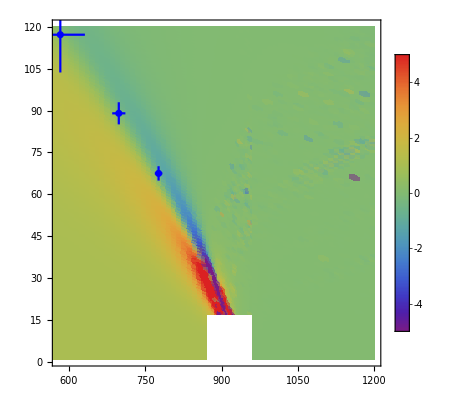

```mathematica
Show[ListDensityPlot[{r42low,r42high,r42high3},PlotRange->{{580,1200},All,{-5,5}},ColorFunction->"Rainbow",PlotLegends->Automatic,ClippingStyle->Automatic],ErrorListPlot[{{{mubcen[[1]],Tcen[[1]]},ErrorBar[muberr[[1]],Terr[[1]]]},{{mubcen[[2]],Tcen[[2]]},ErrorBar[muberr[[2]],Terr[[2]]]},{{mubcen[[3]],Tcen[[3]]},ErrorBar[muberr[[3]],Terr[[3]]]}},PlotRange->{{500,900},{50,100}},PlotStyle->{Blue}](*Plot[{a+b x^2+c x^4/.{a->184.9200925047103,b->-0.00020506323990688002,c->1.6832481767657612*^-11},a+b x^2+c x^4+3/.{a->184.9200925047103,b->-0.00020506323990688002,c->1.6832481767657612*^-11},a+b x^2+c x^4-3/.{a->184.9200925047103,b->-0.00020506323990688002,c->1.6832481767657612*^-11},a+b x^2+c x^4-10/.{a->184.9200925047103,b->-0.00020506323990688002,c->1.6832481767657612*^-11}},{x,580,1000}]*)(*,ListLinePlot[chipeakT,PlotStyle->Red]*)]
```

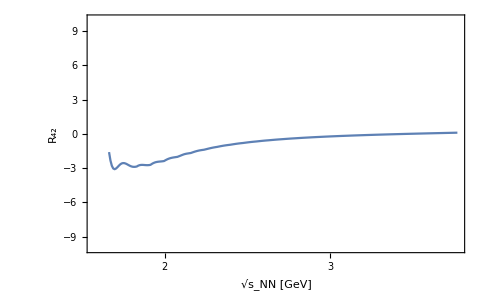

```mathematica
ListLinePlot[{Table[Transpose[{-(125. (-2615.+2. x))/(72. x),f[x,a+b x^2+c x^4+1/.{a->184.9200925047103,b->-0.00020506323990688002,c->1.6832481767657612*^-11}]}],{x,600,870}](*,
Table[Transpose[{-(125. (-2615.+2. x))/(72. x),f[x,a+b x^2+c x^4+3/.{a->184.9200925047103,b->-0.00020506323990688002,c->1.6832481767657612*^-11}]}],{x,700,870}],Table[Transpose[{-(125. (-2615.+2. x))/(72. x),f[x,a+b x^2+c x^4-3/.{a->184.9200925047103,b->-0.00020506323990688002,c->1.6832481767657612*^-11}]}],{x,700,870}],Table[Transpose[{-(125. (-2615.+2. x))/(72. x),f[x,a+b x^2+c x^4-4/.{a->184.9200925047103,b->-0.00020506323990688002,c->1.6832481767657612*^-11}]}],{x,700,870}]*)(*,Table[Transpose[{-(125. (-2615.+2. x))/(72. x),f[x,fchi2peak[x]]}],{x,630,870}]*)}
,PlotRange->{All,{-10,10}},ScalingFunctions->{"Log"},Frame->True,FrameLabel->{"√s_NN [GeV]","R_42"},FrameStyle->Directive[Black,12],LabelStyle->Directive[14]]
```

## Find freeze-out T & μ_B with fRG data

## fRG DATA

```mathematica
frgchi1p1=Import["./fRG_data/chi1data_part1.dat"];
frgchi2p1=Import["./fRG_data/chi2data_part1.dat"];
frgchi3p1=Import["./fRG_data/chi3data_part1.dat"];
frgchi4p1=Import["./fRG_data/chi4data_part1.dat"];
frgchi1p2=Import["./fRG_data/chi1data_part2.dat"];
frgchi2p2=Import["./fRG_data/chi2data_part2.dat"];
frgchi3p2=Import["./fRG_data/chi3data_part2.dat"];
frgchi4p2=Import["./fRG_data/chi4data_part2.dat"];
frgT=Table[i,{i,1,250}];
frgmub1=Flatten[Import["./fRG_data/mub1.dat"]];
frgmub2=Flatten[Import["./fRG_data/mub2.dat"]];
r21frgp1=frgchi2p1/frgchi1p1//Quiet;
r31frgp1=frgchi3p1/frgchi1p1//Quiet;
r42frgp1=frgchi4p1/frgchi2p1//Quiet;
r21frgp2=frgchi2p2/frgchi1p2//Quiet;
r31frgp2=frgchi3p2/frgchi1p2//Quiet;
r42frgp2=frgchi4p2/frgchi2p2//Quiet;
r21frgp1all=Flatten[Table[{x=frgmub1[[j]],y=frgT[[i]],r21frgp1[[j]][[i]]},{i,1,250},{j,1,33}],1];
r21frgp2all=Flatten[Table[{x=frgmub2[[j]],y=frgT[[i]],r21frgp2[[j]][[i]]},{i,1,250},{j,1,Length[frgmub2]}],1];
r31frgp1all=Flatten[Table[{x=frgmub1[[j]],y=frgT[[i]],r31frgp1[[j]][[i]]},{i,1,250},{j,1,33}],1];
r31frgp2all=Flatten[Table[{x=frgmub2[[j]],y=frgT[[i]],r31frgp2[[j]][[i]]},{i,1,250},{j,1,Length[frgmub2]}],1];
fr21frgp1=Interpolation[Flatten[{r21frgp1all,r21frgp2all},1],InterpolationOrder->1];
fr31frgp1=Interpolation[Flatten[{r31frgp1all,r31frgp2all},1],InterpolationOrder->1];
```

## √s_NN=200GeV

```mathematica
z21up=R21BESIcen+R21BESIerr;
z21down=R21BESIcen-R21BESIerr;
z31up=R31BESIcen+R31BESIerr;
z31down=R31BESIcen-R31BESIerr;
```

```mathematica
z21up[[-1]]
z21down[[-1]]
```

6.70234

6.52186

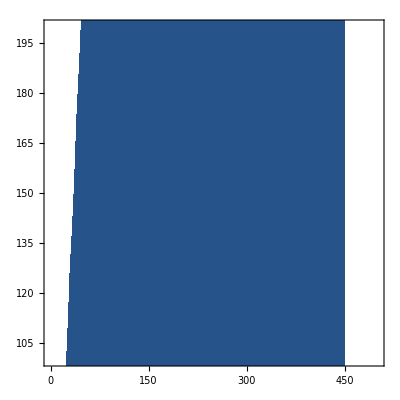

```mathematica
ListContourPlot[{r21frgp1all},Contours->{z21up[[-1]],z21down[[-1]]},PlotRange->{{0,500},{100,200}}]
```

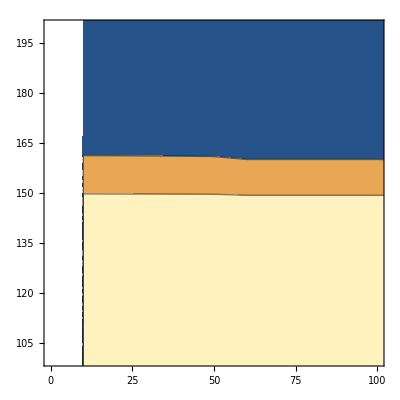

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[-1]],z31down[[-1]]},PlotRange->{{0,100},{100,200}}]
```

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,10,100},{y,145,170},Contours->{z21up[[-1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,10,100},{y,145,170},Contours->{z21down[[-1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,10,100},{y,145,170},Contours->{z31up[[-1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,10,100},{y,145,170},Contours->{z31down[[-1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

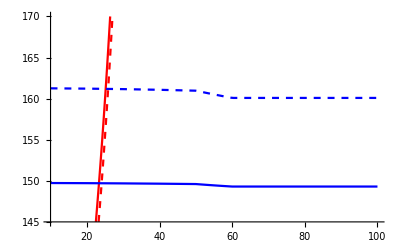

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{10,100},{145,170}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,25}]
intR21up[x1]/.%
```

{x1→23.3343}

149.704

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,25}]
intR21down[x1]/.%
```

{x1→25.8559}

161.182

## √s_NN=62.4GeV

```mathematica
z21up=R21BESIcen+R21BESIerr;
z21down=R21BESIcen-R21BESIerr;
z31up=R31BESIcen+R31BESIerr;
z31down=R31BESIcen-R31BESIerr;
```

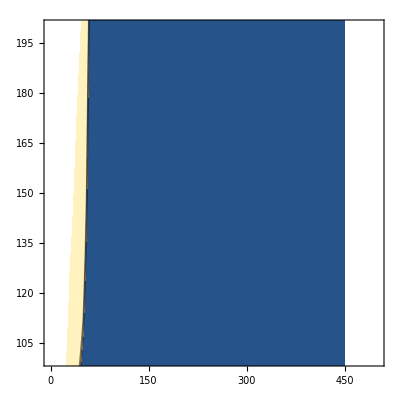

```mathematica
ListContourPlot[{r21frgp1all},Contours->{z21up[[-2]],z21down[[-2]]},PlotRange->{{0,500},{100,200}}]
```

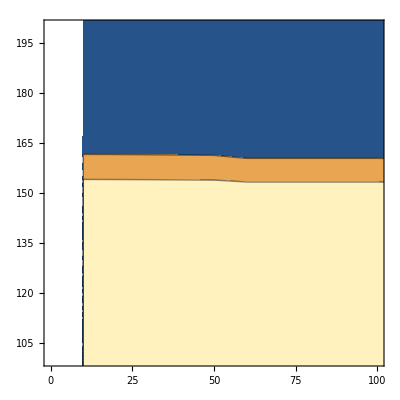

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[-2]],z31down[[-2]]},PlotRange->{{0,100},{100,200}}]
```

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,10,100},{y,145,170},Contours->{z21up[[-2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,10,100},{y,145,170},Contours->{z21down[[-2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,10,100},{y,145,170},Contours->{z31up[[-2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,10,100},{y,145,170},Contours->{z31down[[-2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

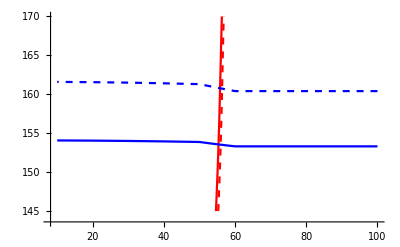

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->All,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,55}]
intR21up[x1]/.%
```

{x1→55.3361}

153.562

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,56}]
intR21down[x1]/.%
```

{x1→56.3287}

160.73

## √s_NN=54.4GeV

```mathematica
z21up=R21BESIcen+R21BESIerr;
z21down=R21BESIcen-R21BESIerr;
z31up=R31BESIcen+R31BESIerr;
z31down=R31BESIcen-R31BESIerr;
```

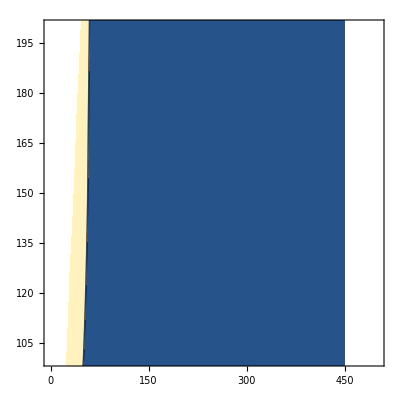

```mathematica
ListContourPlot[{r21frgp1all},Contours->{z21up[[-3]],z21down[[-3]]},PlotRange->{{0,500},{100,200}}]
```

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[-3]],z31down[[-3]]},PlotRange->{{0,100},{100,200}}]
```

-Graphics-

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,10,100},{y,145,170},Contours->{z21up[[-3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,10,100},{y,145,170},Contours->{z21down[[-3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,10,100},{y,145,170},Contours->{z31up[[-3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,10,100},{y,145,170},Contours->{z31down[[-3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{55,70},{150,165}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,57}]
intR21up[x1]/.%
```

{x1→57.1248}

156.022

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,57}]
intR21down[x1]/.%
```

{x1→57.5368}

160.165

## √s_NN=39GeV

```mathematica
z21up=R21BESIcen+R21BESIerr;
z21down=R21BESIcen-R21BESIerr;
z31up=R31BESIcen+R31BESIerr;
z31down=R31BESIcen-R31BESIerr;
```

```mathematica
ListContourPlot[{r21frgp1all},Contours->{z21up[[-4]],z21down[[-4]]},PlotRange->{{0,500},{100,200}}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[-4]],z31down[[-4]]},PlotRange->{{0,100},{100,200}}]
```

-Graphics-

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,10,150},{y,145,170},Contours->{z21up[[-4]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,10,150},{y,145,170},Contours->{z21down[[-4]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,10,150},{y,145,170},Contours->{z31up[[-4]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,10,150},{y,145,170},Contours->{z31down[[-4]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{100,120},{150,165}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,105}]
intR21up[x1]/.%
```

{x1→104.533}

155.756

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,109}]
intR21down[x1]/.%
```

{x1→108.55}

159.758

## √s_NN=27GeV

```mathematica
z21up=R21BESIcen+R21BESIerr;
z21down=R21BESIcen-R21BESIerr;
z31up=R31BESIcen+R31BESIerr;
z31down=R31BESIcen-R31BESIerr;
```

```mathematica
ListContourPlot[{r21frgp1all},Contours->{z21up[[-5]],z21down[[-5]]},PlotRange->{{0,500},{100,200}}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[-5]],z31down[[-5]]},PlotRange->{{0,100},{100,200}}]
```

-Graphics-

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,140,200},{y,145,170},Contours->{z21up[[-5]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,140,200},{y,145,170},Contours->{z21down[[-5]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,50,200},{y,145,170},Contours->{z31up[[-5]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,50,200},{y,145,170},Contours->{z31down[[-5]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up[[90;;-1]],R21down[[50;;-80]],R31up,R31down},PlotRange->{{146,148.1},{150,165}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up[[90;;-1]],InterpolationOrder->3];
intR21down=Interpolation[R21down[[50;;-80]],InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,147}]
intR21up[x1]/.%
```

{x1→147.052}

155.594

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,148.1}]
intR21down[x1]/.%
```

{x1→147.995}

159.197

## √s_NN=19.6GeV (BES-II)

```mathematica
ListContourPlot[Flatten[{r21frgp1all,r21frgp2all},1],Contours->{z21up[[6]],z21down[[6]]},PlotRange->{{100,300},{130,165}}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[6]],z31down[[6]]},PlotRange->{{100,500},{130,165}}]
```

$Aborted

```mathematica
z21up=R21BESIIcen+R21BESIIerr;
z21down=R21BESIIcen-R21BESIIerr;
z31up=R31BESIIcen+R31BESIIerr;
z31down=R31BESIIcen-R31BESIIerr;
```

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,150,300},{y,145,160},Contours->{z21up[[6]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,150,300},{y,145,160},Contours->{z21down[[6]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,150,300},{y,145,160},Contours->{z31up[[6]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,150,300},{y,145,160},Contours->{z31down[[6]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{150,300},{145,160}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,215}]
intR21up[x1]/.%
```

{x1→193.322}

156.61

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,215}]
intR21down[x1]/.%
```

{x1→193.969}

157.073

## √s_NN=17.3GeV (BES-II)

```mathematica
ListContourPlot[Flatten[{r21frgp1all,r21frgp2all},1],Contours->{z21up[[5]],z21down[[5]]},PlotRange->{{200,500},{130,165}}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[5]],z31down[[5]]},PlotRange->{{200,500},{130,165}}]
```

-Graphics-

```mathematica
z21up=R21BESIIcen+R21BESIIerr;
z21down=R21BESIIcen-R21BESIIerr;
z31up=R31BESIIcen+R31BESIIerr;
z31down=R31BESIIcen-R31BESIIerr;
```

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21up[[5]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21down[[5]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31up[[5]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31down[[5]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{200,266},{153,160}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,215}]
intR21up[x1]/.%
```

{x1→216.903}

155.655

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,215}]
intR21down[x1]/.%
```

{x1→216.599}

156.29

## √s_NN=14.6 GeV (BES-II)

```mathematica
ListContourPlot[Flatten[{r21frgp1all,r21frgp2all},1],Contours->{z21up[[4]],z21down[[4]]},PlotRange->{{200,500},{130,165}}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[4]],z31down[[4]]},PlotRange->{{200,500},{130,165}}]
```

-Graphics-

```mathematica
z21up=R21BESIIcen+R21BESIIerr;
z21down=R21BESIIcen-R21BESIIerr;
z31up=R31BESIIcen+R31BESIIerr;
z31down=R31BESIIcen-R31BESIIerr;
R21up=Reap[Do[sol=Quiet@FindRoot[fr21frgp1[x,y]==z21up[[4]],{x,450}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
R21down=Reap[Do[sol=Quiet@FindRoot[fr21frgp1[x,y]==z21down[[4]],{x,450}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
R31up=Reap[Do[sol=Quiet@FindRoot[fr31frgp1[x,y]==z31up[[4]],{y,140}];
Sow[{x,y/. sol}],{x,220,500,1}]][[2,1]];
R31down=Reap[Do[sol=Quiet@FindRoot[fr31frgp1[x,y]==z31down[[4]],{x,420}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
```

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21up[[4]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21down[[4]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31up[[4]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31down[[4]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{245,266},{153,156}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
FindRoot[intR21up[x1]==intR31up[x1],{x1,260}]
intR21up[x1]/.%
```

{x1→255.77}

154.187

```mathematica
FindRoot[intR21down[x1]==intR31down[x1],{x1,260}]
intR21down[x1]/.%
```

{x1→255.712}

154.607

## √s_NN=11.5 GeV (BES-II)

```mathematica
ListContourPlot[Flatten[{r21frgp1all,r21frgp2all},1],Contours->{z21up[[3]],z21down[[3]]},PlotRange->{{200,500},{130,160}}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[3]],z31down[[3]]},PlotRange->{{200,500},{130,160}}]
```

-Graphics-

```mathematica
z21up=R21BESIIcen+R21BESIIerr;
z21down=R21BESIIcen-R21BESIIerr;
z31up=R31BESIIcen+R31BESIIerr;
z31down=R31BESIIcen-R31BESIIerr;
R21up=Reap[Do[sol=Quiet@FindRoot[fr21frgp1[x,y]==z21up[[3]],{x,450}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
R21down=Reap[Do[sol=Quiet@FindRoot[fr21frgp1[x,y]==z21down[[3]],{x,450}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
R31up=Reap[Do[sol=Quiet@FindRoot[fr31frgp1[x,y]==z31up[[3]],{y,140}];
Sow[{x,y/. sol}],{x,220,500,1}]][[2,1]];
R31down=Reap[Do[sol=Quiet@FindRoot[fr31frgp1[x,y]==z31down[[3]],{x,420}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
```

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21up[[3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21down[[3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31up[[3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31down[[3]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{200,550},{120,160}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
dis[x21_,x31_]:=√((x21-x31)^2+(intR21up[x21]-intR31up[x31])^2)
dis2[x21_,x31_]:=√((x21-x31)^2+(intR21down[x21]-intR31down[x31])^2)
sol=NMinimize[{dis[x21,x31],250<=x21<=350&&250<=x31<=350},{x21,x31}]
sol2=NMinimize[{dis2[x21,x31],250<=x21<=350&&250<=x31<=350},{x21,x31}]
```

{1.16188,{x21→323.603,x31→323.52}}

{1.13,{x21→323.14,x31→323.059}}

## √s_NN=9.2 GeV (BES-II)

```mathematica
ListContourPlot[Flatten[{r21frgp1all,r21frgp2all},1],Contours->{z21up[[2]],z21down[[2]]},PlotRange->{{200,500},{130,160}}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[2]],z31down[[2]]},PlotRange->{{200,500},{130,160}}]
```

-Graphics-

```mathematica
z21up=R21BESIIcen+R21BESIIerr;
z21down=R21BESIIcen-R21BESIIerr;
z31up=R31BESIIcen+R31BESIIerr;
z31down=R31BESIIcen-R31BESIIerr;
R21up=Reap[Do[sol=Quiet@FindRoot[fr21frgp1[x,y]==z21up[[2]],{x,450}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
R21down=Reap[Do[sol=Quiet@FindRoot[fr21frgp1[x,y]==z21down[[2]],{x,450}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
R31up=Reap[Do[sol=Quiet@FindRoot[fr31frgp1[x,y]==z31up[[2]],{y,140}];
Sow[{x,y/. sol}],{x,220,500,1}]][[2,1]];
R31down=Reap[Do[sol=Quiet@FindRoot[fr31frgp1[x,y]==z31down[[2]],{x,420}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
```

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21up[[2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21down[[2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31up[[2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31down[[2]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{200,550},{120,160}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
dis[x21_,x31_]:=√((x21-x31)^2+(intR21up[x21]-intR31up[x31])^2)
dis2[x21_,x31_]:=√((x21-x31)^2+(intR21down[x21]-intR31down[x31])^2)
sol=NMinimize[{dis[x21,x31],250<=x21<=350&&250<=x31<=350},{x21,x31}]
sol2=NMinimize[{dis2[x21,x31],250<=x21<=350&&250<=x31<=350},{x21,x31}]
```

{2.05864,{x21→337.841,x31→337.691}}

{2.01866,{x21→336.589,x31→336.436}}

## √s_NN=7.7 GeV (BES-II)

```mathematica
ListContourPlot[Flatten[{r21frgp1all,r21frgp2all},1],Contours->{z21up[[1]],z21down[[1]]},PlotRange->{{200,500},{130,160}}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[{r31frgp1all,r31frgp2all},1],Contours->{z31up[[1]],z31down[[1]]},PlotRange->{{200,500},{130,160}}]
```

-Graphics-

```mathematica
z21up=R21BESIIcen+R21BESIIerr;
z21down=R21BESIIcen-R21BESIIerr;
z31up=R31BESIIcen+R31BESIIerr;
z31down=R31BESIIcen-R31BESIIerr;
R21up=Reap[Do[sol=Quiet@FindRoot[fr21frgp1[x,y]==z21up[[1]],{x,450}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
R21down=Reap[Do[sol=Quiet@FindRoot[fr21frgp1[x,y]==z21down[[1]],{x,450}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
R31up=Reap[Do[sol=Quiet@FindRoot[fr31frgp1[x,y]==z31up[[1]],{y,140}];
Sow[{x,y/. sol}],{x,220,500,1}]][[2,1]];
R31down=Reap[Do[sol=Quiet@FindRoot[fr31frgp1[x,y]==z31down[[1]],{x,420}];
Sow[{x/. sol,y}],{y,130,160,1}]][[2,1]];
```

```mathematica
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21up[[1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr21frgp1[x,y],{x,200,550},{y,120,160},Contours->{z21down[[1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R21down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31up[[1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31up=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
cp=ContourPlot[fr31frgp1[x,y],{x,200,550},{y,120,160},Contours->{z31down[[1]]},ContourShading->False,PlotPoints->50,MaxRecursion->3];
R31down=Flatten[Cases[Normal[cp],Line[p_]:>p,Infinity],1];
```

```mathematica
Show[ListLinePlot[{R21up,R21down,R31up,R31down},PlotRange->{{200,550},{120,160}},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}}](*,ListPlot[{{324.015,intR21up[324.015]},{323.933,intR31up[323.933]}}],ListPlot[{{323.226,intR21down[323.226]},{323.145,intR31down[323.145]}}],ListPlot[{{(324.015+323.933)/2,(intR21up[324.015]+intR31up[323.933])/2},{(323.226+323.145)/2,(intR21down[323.226]+intR31down[323.145])/2}}]*)]
```

-Graphics-

```mathematica
intR21up=Interpolation[R21up,InterpolationOrder->3];
intR21down=Interpolation[R21down,InterpolationOrder->3];
intR31up=Interpolation[R31up,InterpolationOrder->3];
intR31down=Interpolation[R31down,InterpolationOrder->3];
```

```mathematica
dis[x21_,x31_]:=√((x21-x31)^2+(intR21up[x21]-intR31up[x31])^2)
dis2[x21_,x31_]:=√((x21-x31)^2+(intR21down[x21]-intR31down[x31])^2)
sol=NMinimize[{dis[x21,x31],250<=x21<=350&&250<=x31<=350},{x21,x31}]
sol2=NMinimize[{dis2[x21,x31],250<=x21<=350&&250<=x31<=350},{x21,x31}]
```

{2.32902,{x21→345.852,x31→345.68}}

{2.18685,{x21→337.261,x31→337.095}}